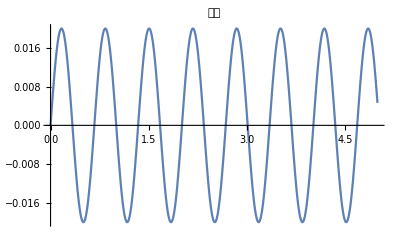
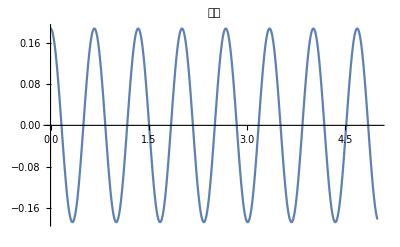
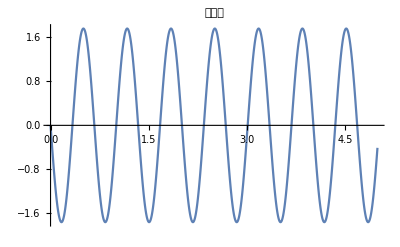

```mathematica
ClearAll["Global`*"];
A=2/100;
T=670/1000;
w=2π/T;

{ListPlot[Table[{t,A*Sin[w*t]},{t,0,5,0.001}],Joined->True,PlotLabel->"変位"],
ListPlot[Table[{t,A*w*Cos[w*t]},{t,0,5,0.001}],Joined->True,PlotLabel->"速度"],
ListPlot[Table[{t,-A*w^2*Sin[w*t]},{t,0,5,0.001}],Joined->True,PlotLabel->"加速度"]}
```

```mathematica
(2*π)/{5.59,
7.56,
8.70,
8.95,
9.37,
9.70,
9.90}
```

{1.124,0.831109,0.722205,0.702032,0.670564,0.647751,0.634665}